# MFEM Mesh Generation

Instructions:
Use mesh tools to create an ElementMesh object for the mesh that you want. 
Set the proper conditions for the BoundaryElement attributes.
For 2D write “2” after numVertices.
Set the proper numbers for element type and boundary element type. 
Set the proper dimension.
Add all the relevant boundaryElement lists.
Export.

```mathematica
<<NDSolve`FEM`
<<MeshTools`
(*<<Notation`*)
<< HKLaTeXWrite`
```

## 2D meshes

## Small Square. Quads

```mathematica
<<NDSolve`FEM`
<<MeshTools`
<<Notation`
<< HKLaTeXWrite`
```

```mathematica
a = 0.1;
```

ElementMesh[{{0.,0.1},{0.,0.1}},{QuadElement[<1600>]}]

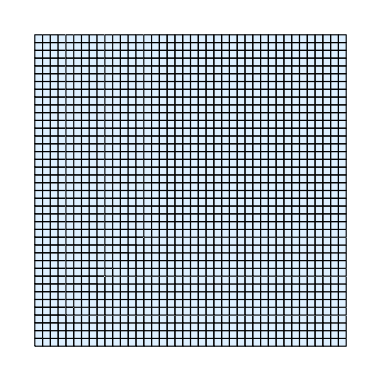

```mathematica
mesh =RectangleMesh[{0,0},{a,a},{40,40}]
Show[mesh["Wireframe"["MeshElementStyle"->FaceForm[LightBlue]]]]
```

```mathematica
coords=mesh["Coordinates"]//Chop[#,10^-7]&;
elements=mesh[[2,1,1]];
```

```mathematica
numVertices=Length[coords];
numElements=Length[elements]
```

1600

### Boundary Element sections

```mathematica
(*Optional:boundary data*)
boundaryElements=mesh["BoundaryElements"][[1,1]];
numBoundary=Length[boundaryElements]
```

160

```mathematica
boundaryElements[[1;;15]]
```

{{1,42},{2,1},{3,2},{4,3},{5,4},{6,5},{7,6},{8,7},{9,8},{10,9},{11,10},{12,11},{13,12},{14,13},{15,14}}

```mathematica
(* Assign boundary attributes *)
```

```mathematica
(* boundary at Y=0 *)
boundaryElements1 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]]<= 0.00001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at Y=1 *)
boundaryElements2 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]] >= (a-0.0001) , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at X=0 *)
boundaryElements3 = Module[{elcoords,belements,zcoords,count},
belements={};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]] <= 0.0001, count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at x=a *)
boundaryElements4 := Module[{elcoords,belements,zcoords,count},
belements={};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]] >= (a-0.0001), count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
]
```

```mathematica
boundaryElements//Length
Total@(Length/@{boundaryElements1,boundaryElements2,boundaryElements3,boundaryElements4})
```

160

160

MFEM Geometry types:
# POINT       		= 0
# SEGMENT     		= 1
# TRIANGLE    		= 2
# SQUARE      		= 3
# TETRAHEDRON 	= 4
# CUBE        		= 5

```mathematica
(*Build vertex section*)
vertexSection=StringJoin["vertices\n",ToString[numVertices],"\n",ToString[2],"\n",StringJoin[Table[StringJoin[ToString[NumberForm[x[[1]],7]]," ",ToString[NumberForm[x[[2]],7]],"\n"],{x,coords}]]];
```

```mathematica
(*Build elements section*)
elementSection1=StringJoin["elements\n",ToString[numElements],"\n",StringJoin[Table[StringJoin["1 3 ",(*1=region attr,2=triangle, 3=square, 4=tetrahedron, 5=cuboid*)StringRiffle[ToString/@(elem-1)," "],"\n"],{elem,elements}]]];
```

```mathematica
(*Boundary section*)
boundarySection1=StringJoin["boundary\n",ToString[numBoundary],"\n",StringJoin[Table[StringJoin["1 1 ",(*1=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements1}]]];
```

```mathematica
boundarySection2=StringJoin[
StringJoin[Table[StringJoin["2 1 ",(*2=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements2}]]];
```

```mathematica
boundarySection3=StringJoin[
StringJoin[Table[StringJoin["3 1 ",(*3=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements3}]]];
```

```mathematica
boundarySection4=StringJoin[
StringJoin[Table[StringJoin["4 1 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements4}]]];
```

```mathematica
mfemMeshContent=StringJoin["MFEM mesh v1.0\n\n","dimension\n"<>"2"<>"\n\n",elementSection1,"\n",boundarySection1,boundarySection2,boundarySection3,boundarySection4,"\n",vertexSection]; (* Set the dimension appropriately *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM/projects/VariationalFracture/scripts

```mathematica
Export["../input/meshes/Square12cm-quad.mesh",mfemMeshContent,"Text"]
```

../input/meshes/Square12cm-quad.mesh

## Square with side slit. Unstructured mesh. Triangles

```mathematica
<<NDSolve`FEM`
<<MeshTools`
<< HKLaTeXWrite`
```

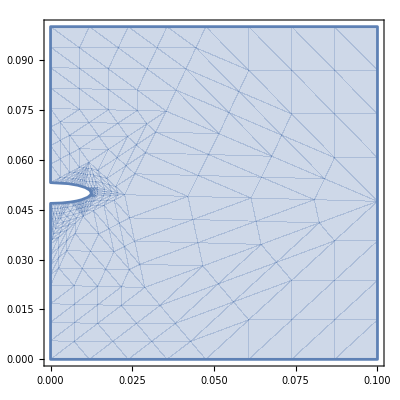

```mathematica
a=0.1;
region=ImplicitRegion[(0<=x<=a)&&(0<=y<=a)&&((x)^2+(y-0.05)^2/0.25^2>=0.0125^2),{x,y}];
RegionPlot[region]
```

ElementMesh[{{0.,0.1},{0.,0.1}},{TriangleElement[<3378>]}]

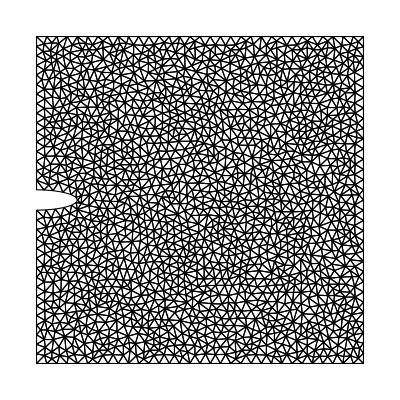

```mathematica
mesh=ToElementMesh[region,MaxCellMeasure->{"Volume"->10^-8},"MeshElementType"->"TriangleElement","MeshOrder"->1]
mesh["Wireframe"]
```

```mathematica
coords=mesh["Coordinates"]//Chop[#,10^-7]&;
elements=mesh[[2,1,1]];
```

```mathematica
numVertices=Length[coords];
numElements=Length[elements]
```

3378

### Boundary Element sections

```mathematica
(*Optional:boundary data*)
boundaryElements=mesh["BoundaryElements"][[1,1]];
numBoundary=Length[boundaryElements]
```

140

```mathematica
boundaryElements[[1;;15]]
```

{{68,1},{69,68},{70,69},{71,70},{72,71},{73,72},{74,73},{75,74},{76,75},{77,76},{78,77},{79,78},{80,79},{81,80},{82,81}}

```mathematica
(* Assign boundary attributes *)
```

```mathematica
(* boundary at Y=0 *)
boundaryElements1 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]]<= 0.00001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at Y=1 *)
boundaryElements2 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]] >= (a-0.0001) , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(*(* boundary at X=0 *)
boundaryElements3 = Module[{elcoords,belements,zcoords,count},
belements={};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]] <= 0.0001, count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];*)
```

```mathematica
(* boundary at x=a *)
boundaryElements4 = Module[{elcoords,belements,zcoords,count},
belements={};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]] >= (a-0.0001), count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
boundaryElements3=UniqueElements[{boundaryElements,Join[boundaryElements1,boundaryElements2,boundaryElements4]}][[1]];
```

```mathematica
boundaryElements//Length
Total@(Length/@{boundaryElements1,boundaryElements2,boundaryElements3,boundaryElements4})
```

140

140

MFEM Geometry types:
# POINT       		= 0
# SEGMENT     		= 1
# TRIANGLE    		= 2
# SQUARE      		= 3
# TETRAHEDRON 	= 4
# CUBE        		= 5

```mathematica
(*Build vertex section*)
vertexSection=StringJoin["vertices\n",ToString[numVertices],"\n",ToString[2],"\n",StringJoin[Table[StringJoin[ToString[NumberForm[x[[1]],7]]," ",ToString[NumberForm[x[[2]],7]],"\n"],{x,coords}]]];
```

```mathematica
(*Build elements section*)
elementSection1=StringJoin["elements\n",ToString[numElements],"\n",StringJoin[Table[StringJoin["1 2 ",(*1=region attr,2=triangle, 3=square, 4=tetrahedron, 5=cuboid*)StringRiffle[ToString/@(elem-1)," "],"\n"],{elem,elements}]]];
```

```mathematica
(*Boundary section*)
boundarySection1=StringJoin["boundary\n",ToString[numBoundary],"\n",StringJoin[Table[StringJoin["1 1 ",(*1=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements1}]]];
```

```mathematica
boundarySection2=StringJoin[
StringJoin[Table[StringJoin["2 1 ",(*2=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements2}]]];
```

```mathematica
boundarySection3=StringJoin[
StringJoin[Table[StringJoin["3 1 ",(*3=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements3}]]];
```

```mathematica
boundarySection4=StringJoin[
StringJoin[Table[StringJoin["4 1 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements4}]]];
```

```mathematica
mfemMeshContent=StringJoin["MFEM mesh v1.0\n\n","dimension\n"<>"2"<>"\n\n",elementSection1,"\n",boundarySection1,boundarySection2,boundarySection3,boundarySection4,"\n",vertexSection]; (* Set the dimension appropriately *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM/projects/VariationalFracture/scripts

```mathematica
Export["../input/meshes/SquareWithSlit-tri.mesh",mfemMeshContent,"Text"]
```

../input/meshes/SquareWithSlit-tri.mesh

## 3D meshes

## Plate with side slit. Unstructured mesh. Tets

```mathematica
<<NDSolve`FEM`
<<MeshTools`
<< HKLaTeXWrite`
```

```mathematica
a=0.1;
t=0.005;
region=ImplicitRegion[(0<=x<=a)&&(0<=y<=a)&&(0<=z<=t)&&((x)^2+(y-0.05)^2/0.125^2+(z-0.0025)^2>=0.0125^2),{x,y,z}];
Show[DiscretizeRegion[region],ViewPoint->Above]
```

-Graphics3D-

```mathematica
mesh=ToElementMesh[region,MaxCellMeasure->{"Volume"->10^-8},"MeshElementType"->"TetrahedronElement","MeshOrder"->1]
Show[mesh["Wireframe"],ViewPoint->Above]
```

ElementMesh[{{0.,0.1},{0.,0.1},{0.,0.005}},{TetrahedronElement[<27414>]}]

-Graphics3D-

```mathematica
coords=mesh["Coordinates"]//Chop[#,10^-7]&;
elements=mesh[[2,1,1]];
```

```mathematica
numVertices=Length[coords];
numElements=Length[elements]
```

27414

### Boundary Element sections

```mathematica
(*Optional:boundary data*)
boundaryElements=mesh["BoundaryElements"][[1,1]];
numBoundary=Length[boundaryElements]
```

15028

```mathematica
boundaryElements[[1;;15]]
```

{{4660,4474,4470},{4658,4660,4470},{4476,4661,4472},{4661,4659,4472},{4662,4478,4474},{4662,4474,4660},{4480,4663,4476},{4663,4661,4476},{4664,4482,4478},{4664,4478,4662},{4484,4665,4480},{4665,4663,4480},{4666,4486,4482},{4666,4482,4664},{4488,4667,4484}}

```mathematica
(* Assign boundary attributes *)
```

```mathematica
(* boundary at Y=0 *)
boundaryElements1 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]]<= 0.00001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at Y=a *)
boundaryElements2 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]] >= (a-0.0001) , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(*(* boundary at X=0 *)
boundaryElements3 = Module[{elcoords,belements,zcoords,count},
belements={};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]] <= 0.0001, count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];*)
```

```mathematica
(*(* boundary at x=a *)
boundaryElements4 = Module[{elcoords,belements,zcoords,count},
belements={};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]] >= (a-0.0001), count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];*)
```

```mathematica
boundaryElements3=UniqueElements[{boundaryElements,Join[boundaryElements1,boundaryElements2]}][[1]];
```

```mathematica
boundaryElements//Length
(Length/@{boundaryElements1,boundaryElements2,boundaryElements3})
```

15028

{911,931,13186}

MFEM Geometry types:
# POINT       		= 0
# SEGMENT     		= 1
# TRIANGLE    		= 2
# SQUARE      		= 3
# TETRAHEDRON 	= 4
# CUBE        		= 5

```mathematica
(*Build vertex section*)
vertexSection=StringJoin["vertices\n",ToString[numVertices],"\n",ToString[3],"\n",StringJoin[Table[StringJoin[ToString[NumberForm[x[[1]],7]]," ",ToString[NumberForm[x[[2]],7]]," ",ToString[NumberForm[x[[3]],7]],"\n"],{x,coords}]]];
```

```mathematica
(*Build elements section*)
elementSection1=StringJoin["elements\n",ToString[numElements],"\n",StringJoin[Table[StringJoin["1 4 ",(*1=region attr,2=triangle, 3=square, 4=tetrahedron, 5=cuboid*)StringRiffle[ToString/@(elem-1)," "],"\n"],{elem,elements}]]];
```

```mathematica
(*Boundary section*)
boundarySection1=StringJoin["boundary\n",ToString[numBoundary],"\n",StringJoin[Table[StringJoin["1 2 ",(*1=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements1}]]];
```

```mathematica
boundarySection2=StringJoin[
StringJoin[Table[StringJoin["2 2 ",(*2=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements2}]]];
```

```mathematica
boundarySection3=StringJoin[
StringJoin[Table[StringJoin["3 2 ",(*3=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements3}]]];
```

```mathematica
(*boundarySection4=StringJoin[
StringJoin[Table[StringJoin["4 1 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements4}]]];*)
```

```mathematica
mfemMeshContent=StringJoin["MFEM mesh v1.0\n\n","dimension\n"<>"3"<>"\n\n",elementSection1,"\n",boundarySection1,boundarySection2,boundarySection3,"\n",vertexSection]; (* Set the dimension appropriately *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM/projects/VariationalFracture/scripts

```mathematica
Export["../input/meshes/ThinPlateWithSlit-tet.mesh",mfemMeshContent,"Text"]
```

../input/meshes/ThinPlateWithSlit-tet.mesh

## Slab with bottom notch. Unstructured mesh. Tets

```mathematica
<<NDSolve`FEM`
<<MeshTools`
<< HKLaTeXWrite`
```

```mathematica
a=0.1;
b=0.04;
t=0.005;
trianglebase=0.0025;
triangleheight=0.0075;
region1 = Rectangle[{0,0},{a,b}];
region2 = Triangle[{{a/2,0+triangleheight},{a/2-trianglebase/2,0},{a/2+trianglebase/2,0}}];
region3=RegionDifference[region1,region2];
region4=RegionProduct[region3,Line[{{0},{t}}]];
Region[region4];
```

```mathematica
mesh=ToElementMesh[region4,MaxCellMeasure->{"Volume"->10^-8},"MeshElementType"->"TetrahedronElement","MeshOrder"->1]
Show[mesh["Wireframe"],ViewPoint->{0, 0, 1}]
```

ElementMesh[{{0.,0.1},{0.,0.04},{0.,0.005}},{TetrahedronElement[<4100>]}]

-Graphics3D-

```mathematica
coords=mesh["Coordinates"]//Chop[#,10^-7]&;
elements=mesh[[2,1,1]];
```

```mathematica
numVertices=Length[coords];
numElements=Length[elements]
```

4100

### Boundary Element sections

Boundary elements sections are as follows:
1. Normal vec: (-1,0,0)
2. Normal vec: (1,0,0)
3. Normal vec: (0,-1,0)
4. Normal vec: (0,1,0)
5. Normal vec: (0,0-1)
6. Normal vec: (0,0,1)
7. Notch elements

```mathematica
(*Optional:boundary data*)
boundaryElements=mesh["BoundaryElements"][[1,1]];
numBoundary=Length[boundaryElements]
```

2244

```mathematica
boundaryElements[[1;;15]]
```

{{41,781,481},{241,457,21},{769,1005,471},{375,928,97},{234,45,438},{386,652,205},{692,944,222},{213,1114,14},{821,831,822},{182,359,357},{294,295,3},{616,1102,351},{296,1076,550},{407,1115,121},{619,1102,354}}

```mathematica
(* Assign boundary attributes *)
```

```mathematica
(* boundary at X=0 *)
boundaryElements1 = Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]]<= 0.00001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at X=a *)
boundaryElements2=Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]]>= (a-0.00001) , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at Y=0 *)
boundaryElements3=Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]]<= 0.00001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at Y=b *)
boundaryElements4=Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]]>= (b-0.00001) , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at Z=0 *)
boundaryElements5=Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,3]]<= 0.00001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
(* boundary at Z=t *)
boundaryElements6=Module[{elcoords,belements,zcoords,count},
belements = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,3]]>= (t-0.00001) , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements,i]
 ];
,{i,boundaryElements}];
belements
];
```

```mathematica
boundaryElements7=UniqueElements[{boundaryElements,Join[boundaryElements1,boundaryElements2,boundaryElements3,boundaryElements4,boundaryElements5,boundaryElements6]}][[1]];
```

```mathematica
boundaryElements//Length
Total@(Length/@{boundaryElements1,boundaryElements2,boundaryElements3,boundaryElements4,boundaryElements5,boundaryElements6,boundaryElements7})
```

2244

2244

```mathematica
ListPointPlot3D[{coords[[DeleteDuplicates@(Flatten@boundaryElements1)]],coords[[DeleteDuplicates@(Flatten@boundaryElements2)]],coords[[DeleteDuplicates@(Flatten@boundaryElements3)]],coords[[DeleteDuplicates@(Flatten@boundaryElements4)]],coords[[DeleteDuplicates@(Flatten@boundaryElements7)]]},ViewPoint->{0,0,1},AspectRatio->b/a]
```

-Graphics3D-

MFEM Geometry types:
# POINT       		= 0
# SEGMENT     		= 1
# TRIANGLE    		= 2
# SQUARE      		= 3
# TETRAHEDRON 	= 4
# CUBE        		= 5

```mathematica
(*Build vertex section*)
vertexSection=StringJoin["vertices\n",ToString[numVertices],"\n",ToString[3],"\n",StringJoin[Table[StringJoin[ToString[NumberForm[x[[1]],10]]," ",ToString[NumberForm[x[[2]],10]]," ",ToString[NumberForm[x[[3]],10]],"\n"],{x,coords}]]];
```

```mathematica
(*Build elements section*)
elementSection1=StringJoin["elements\n",ToString[numElements],"\n",StringJoin[Table[StringJoin["1 4 ",(*1=region attr,2=triangle, 3=square, 4=tetrahedron, 5=cuboid*)StringRiffle[ToString/@(elem-1)," "],"\n"],{elem,elements}]]];
```

```mathematica
(*Boundary section*)
boundarySection1=StringJoin["boundary\n",ToString[numBoundary],"\n",StringJoin[Table[StringJoin["1 2 ",(*1=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements1}]]];
```

```mathematica
boundarySection2=StringJoin[
StringJoin[Table[StringJoin["2 2 ",(*2=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements2}]]];
```

```mathematica
boundarySection3=StringJoin[
StringJoin[Table[StringJoin["3 2 ",(*3=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements3}]]];
```

```mathematica
boundarySection4=StringJoin[
StringJoin[Table[StringJoin["4 2 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements4}]]];
```

```mathematica
boundarySection5=StringJoin[
StringJoin[Table[StringJoin["5 2 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements5}]]];
```

```mathematica
boundarySection6=StringJoin[
StringJoin[Table[StringJoin["6 2 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements6}]]];
```

```mathematica
boundarySection7=StringJoin[
StringJoin[Table[StringJoin["7 2 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements7}]]];
```

```mathematica
mfemMeshContent=StringJoin["MFEM mesh v1.0\n\n","dimension\n"<>"3"<>"\n\n",elementSection1,"\n",boundarySection1,boundarySection2,boundarySection3,boundarySection4,boundarySection5,boundarySection6,boundarySection7,"\n",vertexSection]; (* Set the dimension appropriately *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM/projects/VariationalFracture/scripts

```mathematica
Export["../input/meshes/SlabWithNotch2-tet.mesh",mfemMeshContent,"Text"]
```

../input/meshes/SlabWithNotch2-tet.mesh

```mathematica
Ε=20800;
ν=0.3;
λ=(Ε ν)/((1+ν)(1-2ν))
μ=Ε/(2(1+ν))
```

12000.

8000.